## Ricker Model

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/ews_seasonal/ricker_std/bifurcation"];
```

```mathematica
(* Import bifurcation data points *)
bifData = Import["../data_export/bif_data_ricker.csv"];
```

```mathematica
(* Paramters of model *)
k=224; (* carrying capacity from Bentini et al. *)
```

```mathematica
(* Extract growth (r) values and state values *)
rVals=bifData[[1,2;;]];
stateVals=bifData[[2;;,2;;]];
```

```mathematica
(* Normalise state values by carrying capacity (plot x/k) *)
stateValsNorm=stateVals/k;
```

```mathematica
(* Arrange for plotting *)
plotVals=Table[Transpose[{rVals,stateValsNorm[[i]]}],{i,1,Length[stateVals]}];
plotVals//Dimensions
```

{100,1000,2}

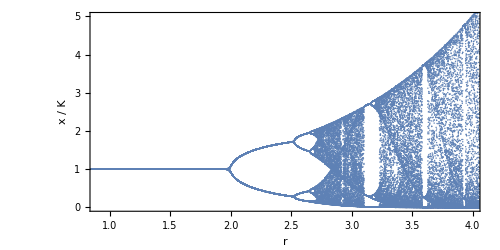

```mathematica
bifRicker=ListPlot[plotVals[[1;;100]],
Frame->True,
FrameLabel->{{"x / K",None},{"r",None}},
PlotRange->{{0.9,4},{0,5}},
PlotStyle->Directive[{TMBcolours[[1]],PointSize[0.002]}],
AspectRatio->0.5,
ImageSize->500,
LabelStyle->14]
```

```mathematica
Export["../figures/bif_ricker.png",bifRicker,ImageResolution->400];
```